```mathematica
g = Import["/Users/isabelfulcher1/Dropbox/01_Research/Research_Eric/Networks/auto_g_networks/revisions/input/adj800miss1.txt","Table"]
```

{1}
 |  |  |  |

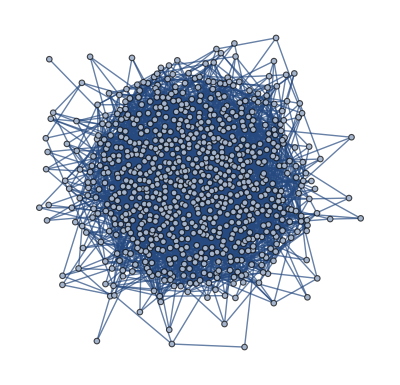

```mathematica
gnew = AdjacencyGraph[g]
```

```mathematica
FindIndependentVertexSet[gnew,800,100000][[1]]
```

{1,2,5,9,12,15,16,17,19,20,22,23,24,25,27,29,30,31,33,36,39,41,45,54,55,56,60,61,66,68,70,71,74,75,80,81,82,84,88,89,91,93,94,95,97,99,100,101,103,104,105,107,109,110,111,112,113,118,119,123,129,133,136,138,139,142,149,151,160,165,167,170,177,181,182,183,184,192,199,201,205,206,208,215,216,221,223,225,227,228,232,237,240,241,253,255,261,264,265,267,270,273,275,289,293,299,303,309,315,319,321,325,326,332,337,339,340,343,344,345,347,349,354,355,357,360,361,363,366,368,369,370,371,373,375,380,381,385,386,387,396,402,409,413,422,424,426,427,428,432,433,434,437,439,442,443,445,450,457,462,471,472,475,478,480,484,488,490,495,498,504,508,511,516,517,520,521,522,524,527,528,531,532,533,543,551,556,561,569,571,576,577,579,580,581,583,595,596,598,599,600,605,613,614,621,624,625,635,636,637,638,641,643,649,651,659,665,668,672,675,677,678,679,682,685,694,699,704,710,713,714,716,731,734,735,736,741,743,747,751,753,758,761,762,764,767,770,771,778,780,784,785,788,791}

```mathematica
Length[FindIndependentVertexSet[gnew,800,100000][[1]]]
```

254

```mathematica
Export["/Users/isabelfulcher1/Dropbox/01_Research/Research_Eric/Networks/auto_g_networks/revisions/input/maxindep800miss1",FindIndependentVertexSet[gnew,800,10000][[1]],"Table"]
```

/Users/isabelfulcher1/Dropbox/01_Research/Research_Eric/Networks/auto_g_networks/revisions/input/maxindep800miss1

```mathematica
Export["/Users/isabelfulcher1/Dropbox/01_Research/Research_Eric/Networks/auto_g_networks/revisions/input/adj800miss1",Normal[AdjacencyMatrix[gnew]],"Table"]
```

/Users/isabelfulcher1/Dropbox/01_Research/Research_Eric/Networks/auto_g_networks/revisions/input/adj800miss1